```mathematica
(* HNNP *)
Z0[x0_,x1_,x2_,x3_,x4_]:=μ^(-(x0*x3+x1*x4)/2)*η^(-(x1+x3)/2)*Exp[-2*A[0]]*A[1]^(-((x0+x1)+(x1+x2)+(x2+x3)+(x3+x4))/2)*A[2]^(-((x0+x2)+(x2+x4))/2)*A[3]^(-(x0*x1+x1*x2+x2*x3+x3*x4)/2)*A[4]^(-(x0*x2+x2*x4)/2)*A[5]^(-(x0*x1*x2+x2*x3*x4)/2)
Z1[x0_,x2_,x4_]:=Exp[-B[0]]*B[1]^(-((x0+x2)+(x2+x4))/2)*B[2]^(-(x0+x4)/2)*B[3]^(-(x0*x2+x2*x4)/2)*B[4]^(-(x0*x4)/2)*B[5]^(-x0*x2*x4/2)
TrZ0[x0_,x2_,x4_]:=Sum[Sum[Z0[x0,x1,x2,x3,x4],{x1,-1,1,2}],{x3,-1,1,2}]
i=0;
For[x0=-1,x0<=1,x0+=2,
For[x2=-1,x2<=1,x2+=2,
For[x4=-1,x4<=1,x4+=2,
leq[i]=Z1[x0,x2,x4];
req[i++]=TrZ0[x0,x2,x4];
]
]
]
(*Equates the unrenormalized with the renormalized variables*)
req[0]==leq[0];
req[1]==leq[1];
req[2]==leq[2];
req[3]==leq[3];
req[4] == leq[4];
req[5] ==leq[5] ;
req[6] ==leq[6] ;
req[7] ==leq[7] ;

Print["Solving for RG equations..."]
SB[0]=Simplify[Part[Solve[Simplify[1/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/8),Assumptions->B[0]>0]==Simplify[1/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/8),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[0]],1]];
SB[0]={B[0]-> 2*A[0]+(B[0]/.SB[0]/.A[0]->0)};
SB[1]=Simplify[Part[Solve[Simplify[((leq[0]*leq[1]*leq[1]*leq[5])^(1/4)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/8)),Assumptions->(B[1]>0 && B[3]>0 && B[0]>0)]==Simplify[((req[0]*req[1]*req[1]*req[5])^(1/4)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/8)),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[1]],1]];
SB[2]=Simplify[Part[Solve[Simplify[((leq[2]/leq[5]/leq[1])^(1/4)*(leq[0]/leq[1]*leq[2]*leq[3]*leq[4]/leq[5]*leq[6]/leq[7])^(1/8)),Assumptions->(B[1]>0 && B[3]>0 && B[0]>0&& B[2]>0&& B[4]>0&& B[5]>0)]==Simplify[((req[2]/req[5]/req[1])^(1/4)*(req[0]/req[1]*req[2]*req[3]*req[4]/req[5]*req[6]/req[7])^(1/8)),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[2]],1]];
SB[3]=Simplify[Part[Solve[Simplify[(leq[2]*leq[5]*leq[1]*leq[3])^(1/2)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4),Assumptions->(B[0]>0 && B[3]>0)]==Simplify[(req[2]*req[5]*req[1]*req[3])^(1/2)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[3]],1]];
SB[4]=Simplify[Part[Solve[Simplify[(leq[1]*leq[3])/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4),Assumptions->B[0]>0]==Simplify[(req[1]*req[3])/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[4]],1]];
SB[5]=Simplify[Part[Solve[Simplify[(leq[0]/leq[1]/leq[2]*leq[3])^(1/2)*((leq[2]*leq[5]*leq[1]*leq[3])^(1/2)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4)),Assumptions->(B[3]>0 && B[5]>0 && B[0]>0)]==Simplify[(req[0]/req[1]/req[2]*req[3])^(1/2)*((req[2]*req[5]*req[1]*req[3])^(1/2)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4)),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[5]],1]];
SBT=Table[Part[Factor[SB[n]],1],{n,0,5}];
Print["Done."]
Print["Setting up RG and W matrix..."]
(* HNNP & HN3:  Sets the initial conditions. *)
(* B[0]=free energy, B[1]=backbone bond magnetization, 
   B[2]=long-range bond magnetization, B[3]=backbone coupling,
   B[4]=long-range coupling, B[5]=three-point operator *)
SIC={B[0]->0,B[1]->1,B[2]->1,B[3]->μ,B[4]->1,B[5]->1};
InitRG:=SAT=Table[A[n]->B[n]/.SIC,{n,0,5}];
RG:=SAT=Table[A[n]->B[n]/.Simplify[SBT/.SAT],{n,0,5}];
W=Table[Factor[D[(B[i]/.SBT),A[j]]],{j,0,5},{i,0,5}];
LnZ1=-A[0]+Log[Sum[Sum[Sum[η^(-(x0+x1+x2)/2)*A[1]^(-((x0+x1)+(x1+x2))/2)*A[2]^(-(x0+x2)/2)*A[3]^(-(x0*x1+x1*x2)/2)*A[4]^(-(x0*x2)/2)*A[5]^(-(x0*x1*x2)/2),{x0,-1,1,2}],{x1,-1,1,2}],{x2,-1,1,2}]];
LnZ1=-A[0]+(LnZ1/.A[0]->0);
LnZ2=FullSimplify[-2*A[0]+Log[Sum[Sum[Sum[Sum[Sum[μ^(-(x0*x3+x1*x4)/2)*η^(-(x0+x1+x2+x3+x4)/2)*A[1]^(-((x0+x1)+(x1+x2)+(x2+x3)+(x3+x4))/2)*A[2]^(-((x0+x2)+(x2+x4))/2)*A[3]^(-(x0*x1+x1*x2+x2*x3+x3*x4)/2)*A[4]^(-(x0*x2+x2*x4)/2)*A[5]^(-(x0*x1*x2+x2*x3*x4)/2),{x0,-1,1,2}],{x1,-1,1,2}],{x2,-1,1,2}],{x3,-1,1,2}],{x4,-1,1,2}]],Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)];
Print["Done."]
```

Solving for RG equations...

Done.

Setting up RG and W matrix...

Done.

```mathematica
InitRG;
FullSimplify[LnZ2/.SAT/.η->1,Assumptions->μ>0]
InitRG;
RG;
FullSimplify[LnZ1/.SAT/.η->1,Assumptions->μ>0]
FullSimplify[%-%%%%,Assumptions->μ>0]
```

-3 Log[μ]+Log[2 (1+μ^2 (3+μ (8+3 μ+μ^3)))]

ConditionalExpression[-2 ⅈ π C[1]-3 Log[μ]+Log[2 (1+μ^2 (3+μ (8+3 μ+μ^3)))],C[1]∈Integers]

ConditionalExpression[-2 ⅈ π C[1],C[1]∈Integers]

```mathematica
InitRG
```

{A[0]→0,A[1]→1,A[2]→1,A[3]→κ,A[4]→1,A[5]→1}

```mathematica
DLnZ2=FullSimplify[Table[Factor[D[LnZ2,A[n]]],{n,0,5}],Assumptions-> (η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)];
DLnZ1=FullSimplify[Table[Factor[D[LnZ1,A[n]]],{n,0,5}],Assumptions-> (η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)];
```

```mathematica
DDLnZ2η=Simplify[D[DLnZ2η,η],Assumptions-> η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0];DDLnZ1η=Simplify[D[DLnZ1η,η],Assumptions-> η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0];
```

```mathematica
FullSimplify[4/5^2*DDLnZ2η/.SAT/.η->1/.μ->κ]
FullSimplify[4/3^2*DDLnZ1η/.SAT/.η->1]
```

(25+κ^2 (27+κ (24+3 κ+κ^3)))/(25 (1+κ^2 (3+κ (8+3 κ+κ^3))))

1/9+8/(9 (1+κ)^2)

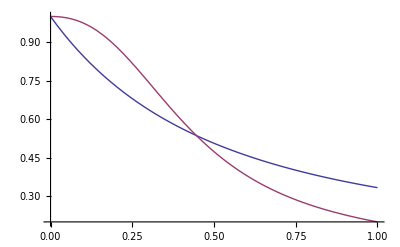

```mathematica
Plot[{%,%%},{κ,0,1}]
```